# Exam Review

#### Q2 (d)

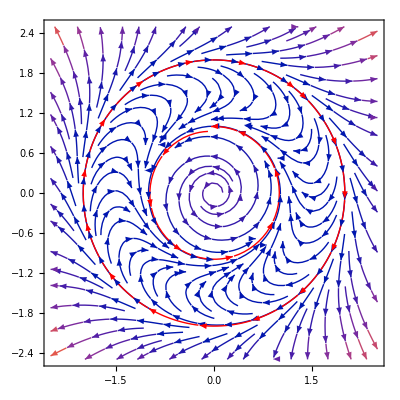

```mathematica
field={r(1-r)(2-r),2(1.5-r) };
p1= StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",field,{r,θ}->{x,y}],{x,-2.5,2.5},{y,-2.5, 2.5}];
p2 = StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",field,{r,θ}->{x,y}],{x,-2.5,2.5},{y,-2.5, 2.5}, StreamPoints->{ {√2,√2}, {0, 1}}, StreamColorFunction->None, StreamStyle->Red, StreamScale->Large];
Show[p1, p2]
```

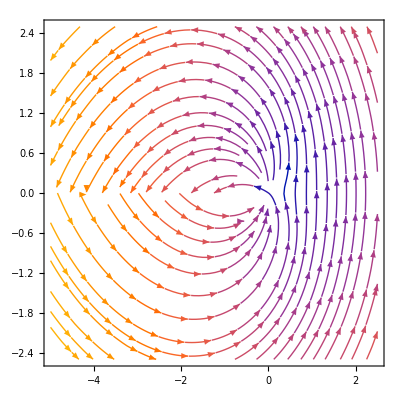

```mathematica
field={θ, r};
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",field,{r,θ}->{x,y}],{x,-5,2.5},{y,-2.5, 2.5}]
```

```mathematica
f[x_, r_]:= -x - r Tanh[x]
```

```mathematica
D[f[x, r], x]
```

-1-r Sech[x]^2

```mathematica
Series[f[x, r], {x, 0, 3}] // Normal
```

(-1-r) x+(r x^3)/3

```mathematica
Solve[(-1-r) x+(r x^3)/3 == 0 && D[(-1-r) x+(r x^3)/3, x] ==0, {x, r}]
```

{{x→0,r→-1}}